```mathematica
Quit[]
```

#### Kernels Control

```mathematica
LaunchKernels[8]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

```mathematica
CloseKernels[Kernels[]]
```

```mathematica
Kernels[]
```

### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop]];
```

```mathematica
ParallelEvaluate[On[General::stop]];
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="/home/huangys/mount/DATA/Documents/2-d-data";}];
```

```mathematica
Kernel1[ϕn_][x_?NumberQ]:=NIntegrate[ϕn[p]/(p-x)^2,{p,0,1}];
Kernel2[ϕn_,ϕm_][x_?NumberQ,z_?NumberQ,ω_?NumberQ]:=NIntegrate[(ϕn[y]ϕm[z/ω y])/(y-x)^2,{y,0,1}];
```

```mathematica
A[ω_][ϕ1_,ϕ2_,ϕ3_]:=1/(1-ω)NIntegrate[ϕ1[x]ϕ2[x/ω] ϕ3[p]/(p-(x-ω)/(1-ω))^2,{p,0,1},{x,0,ω},Method->"GlobalAdaptive"]-1/ω NIntegrate[ϕ1[x]ϕ3[(x-ω)/(1-ω)] ϕ2[p]/(p-x/ω)^2,{p,0,1},{x,ω,1},Method->"GlobalAdaptive"](*r1=1*)
```

```mathematica
FBBplusDD[z_,ω_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=(1+ℂ)If[ω>z,-HeavisideTheta[ω-z](1-ω)/z(NIntegrate[ϕ4[(1-ω)/(1-z)x]ϕ2[x](ϕ3[y]ϕ1[z/ω y])/(y-(1-(1-x)(1-ω)/z))^2,{x,0,1},{y,0,1-(1-x)(1-ω)/z-λ}]+NIntegrate[ϕ4[(1-ω)/(1-z)x]ϕ2[x](ϕ3[y]ϕ1[z/ω y])/(y-(1-(1-x)(1-ω)/z))^2,{x,0,1},{y,1-(1-x)(1-ω)/z+λ,1},Method->"LocalAdaptive"]-NIntegrate[2ϕ4[(1-ω)/(1-z)x]ϕ2[x]ϕ3[1-(1-x)(1-ω)/z] ϕ1[z/ω(1-(1-x)(1-ω)/z)]/λ,{x,0,1}]),HeavisideTheta[z-ω](1-z)/ω(NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1-(1-x)(1-z)/ω-λ}]+NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,1-(1-x)(1-z)/ω+λ,1},Method->"LocalAdaptive"]-NIntegrate[2ϕ4[(1-z)/(1-ω)x]ϕ2[x]ϕ3[1-(1-x)(1-z)/ω] ϕ1[ω/z(1-(1-x)(1-z)/ω)]/λ,{x,0,1}])]
```

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
Nc=1000;ℂ=0;(*ℂ denotes the interchange of final states.*)λ=10^-6;
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

```mathematica
ω[M1_,M2_,M3_]:=(*-*)(√((M1^2+M2^2-M3^2)^2-4 M1^2 M2^2))/(2 M1^2)+M2^2/(2 M1^2)-M3^2/(2 M1^2)+1/2
```

```mathematica
zfp[ω_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2-M3^2 ω+M4^2 ω))(M3^2+M1^2 ω-M2^2 ω-M3^2 ω+M4^2 ω-M1^2 ω^2+M2^2 ω^2-√(-4 (M3^2-M3^2 ω+M4^2 ω) (M1^2 ω-M1^2 ω^2)+(-M3^2-M1^2 ω+M2^2 ω+M3^2 ω-M4^2 ω+M1^2 ω^2-M2^2 ω^2)^2));
```

```mathematica
zfn[ω_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2-M3^2 ω+M4^2 ω))(M3^2+M1^2 ω-M2^2 ω-M3^2 ω+M4^2 ω-M1^2 ω^2+M2^2 ω^2+√(-4 (M3^2-M3^2 ω+M4^2 ω) (M1^2 ω-M1^2 ω^2)+(-M3^2-M1^2 ω+M2^2 ω+M3^2 ω-M4^2 ω+M1^2 ω^2-M2^2 ω^2)^2))
```

```mathematica
ASin[n_][m1_]:=
Module[{ϕx,m2,ϕ,Vals,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,ωnow,filename},
(*SetSharedVariable[m2,m1];*)
m2=m1;
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
ϕ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx},"TSV"]
},
{
{Vals,ϕx}=Import[dir<>filename,"TSV"];
ϕ[x_]=ϕx;
}
];
{M1,ϕ1}={Mn[#][Vals],ϕn[#][ϕ]}&[n];{M2,ϕ2}={Mn[#][Vals],ϕn[#][ϕ]}&[1];{M3,ϕ3}={Mn[#][Vals],ϕn[#][ϕ]}&[1];
Print[ω[M1,M2,M3]];
Ares=A[ω[M1,M2,M3]][ϕ1,ϕ2,ϕ3];
Print[{m1^2,Ares}];
{m1^2,Ares}
]
```

```mathematica
At[n_][ma_,mb_,δm_]:=Table[
Module[{ϕx,m2,ϕ,Vals,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,ωnow,filename},
(*SetSharedVariable[m2,m1];*)
m2=m1;
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
ϕ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx},"TSV"]
},
{
{Vals,ϕx}=Import[dir<>filename,"TSV"];
ϕ[x_]=ϕx;
}
];
{M1,ϕ1}={Mn[#][Vals],ϕn[#][ϕ]}&[n];{M2,ϕ2}={Mn[#][Vals],ϕn[#][ϕ]}&[1];{M3,ϕ3}={Mn[#][Vals],ϕn[#][ϕ]}&[1];
Print[ω[M1,M2,M3]];
Ares=A[ω[M1,M2,M3]][ϕ1,ϕ2,ϕ3];
Print[{m1^2,Ares}];
{m1^2,Ares}
],{m1,ma,mb,δm}]
```

```mathematica
B2toB0π0[mQ_,mq_]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
m1=mq;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Valsπ,ϕxπ}=Determineϕx[m1,m2,β,Nx];
Set@@{Φπ[x_],ϕxπ};
Export[dir<>filename,{Valsπ,ϕxπ}]
},
{
{Valsπ,ϕxπ}=Import[dir<>filename];
Set@@{Φπ[x_],ϕxπ};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M3,ϕ3}={Mn[#][Valsπ],ϕn[#][Φπ]}&[0];
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
ParallelTable[Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]},{ω,0.1,0.5,0.1}]~Join~ParallelTable[Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]},{ω,0.6,0.8,0.02}]~Join~ParallelTable[Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]},{ω,0.8,0.9,0.01}]~Join~ParallelTable[Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]},{ω,0.9,0.99,0.005}]
]
```

```mathematica
B2π2toB0π0[mQ_,mq_]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4,z},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
m1=mq;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Valsπ,ϕxπ}=Determineϕx[m1,m2,β,Nx];
Set@@{Φπ[x_],ϕxπ};
Export[dir<>filename,{Valsπ,ϕxπ}]
},
{
{Valsπ,ϕxπ}=Import[dir<>filename];
Set@@{Φπ[x_],ϕxπ};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
{M2,ϕ2}={Mn[#][Valsπ],ϕn[#][Φπ]}&[2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][Valsπ],ϕn[#][Φπ]}&[0];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
ParallelTable[z=zfn[ω][M1,M2,M3,M4];If[z∈Reals,Print["z=",z,"    ω=",ω];{ω,FBBplusDD[z,ω][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω=",ω]],{ω,0.1,0.5,0.1}]~Join~ParallelTable[z=zfn[ω][M1,M2,M3,M4];If[z∈Reals,Print["z=",z,"    ω=",ω];{ω,FBBplusDD[z,ω][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω=",ω]],{ω,0.5,0.7,0.03}]~Join~
ParallelTable[z=zfn[ω][M1,M2,M3,M4];If[z∈Reals,Print["z=",z,"    ω=",ω];{ω,FBBplusDD[z,ω][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω=",ω]],{ω,0.7,0.99,0.01}]
]
```

#### Calc

#### 1→2

```mathematica
Clear["Global`g$*"]
```

```mathematica
Information["Global`g$*"]
```

```mathematica
Clear[ϕx,m2,ϕ,vals,M1,M2,M3,ϕ1,ϕ2,ϕ3];
```

```mathematica
ParallelEvaluate[Information[ϕn]]
```

```mathematica
ASin[5][0.5]
```

```mathematica
ωt=B2toB0π0[√2000,√0.3136]
```

Wavefunction build complete.

ω=0.1

ω=0.2

ω=0.3

ω=0.4

ω=0.5

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00142079 and 7.43192×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00116928 and 2.59093×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0011258 and 1.06321×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000672192 and 1.54732×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0337574 and 0.0000113783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00208589 and 1.18318×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0887886 and 0.0000238159 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00374434 and 1.716×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000788288 and 3.82665×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0133981 and 5.05636×10^-6 for the integral and error estimates.

ω=0.6

ω=0.64

ω=0.68

ω=0.72

ω=0.74

ω=0.76

ω=0.78

ω=0.8

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0131395 and 2.58073×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00658711 and 2.1642×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0186183 and 3.55703×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0361582 and 6.67915×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0557438 and 9.74414×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.222678 and 3.1108×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0832324 and 1.37054×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.131037 and 1.9267×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.390407 and 0.0000811307 for the integral and error estimates.

ω=0.66

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0156135 and 2.88654×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.490222 and 0.0000936944 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.246304 and 0.0000587191 for the integral and error estimates.

ω=0.62

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00769527 and 2.10213×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.311405 and 0.000062445 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.637362 and 0.000118703 for the integral and error estimates.

ω=0.7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.10361 and 0.000195256 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0287382 and 4.78606×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.49397 and 0.000260208 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.09428 and 0.000333063 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.48251 and 0.000624085 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.01287 and 0.000419633 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.82684 and 0.000161024 for the integral and error estimates.

ω=0.8

ω=0.82

ω=0.84

ω=0.86

ω=0.87

ω=0.88

ω=0.89

ω=0.9

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.78536 and 0.0000560063 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.28094 and 0.000033979 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.398858 and 6.25835×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.222678 and 3.1108×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.19053 and 0.0000592661 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.3502 and 0.00001738 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.781 and 0.0000297835 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.738637 and 0.0000140671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.48251 and 0.000624085 for the integral and error estimates.

ω=0.81

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.88907 and 0.000895992 for the integral and error estimates.

ω=0.83

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.296329 and 4.06607×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.541615 and 7.48903×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -10.7667 and 0.0010922 for the integral and error estimates.

ω=0.85

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -19.7982 and 0.00155432 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.00444 and 0.000017608 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -16.4692 and 0.00111684 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -22.8748 and 0.00139859 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -24.8436 and 0.00166759 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -24.3932 and 0.00129696 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.53733 and 0.000736425 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.60972 and 0.000981439 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -13.3974 and 0.00123383 for the integral and error estimates.

ω=0.91

ω=0.92

ω=0.93

ω=0.935

ω=0.94

ω=0.945

ω=0.95

ω=0.9

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.19053 and 0.0000592661 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.32847 and 0.0000502922 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.941101 and 0.0000241344 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.19589 and 0.000045892 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.60381 and 0.0000425938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.352163 and 0.0000226418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.264786 and 0.0000262979 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.02809 and 0.0000548063 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 11.731 and 0.001042 for the integral and error estimates.

ω=0.955

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.83675 and 0.0000206682 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19.3819 and 0.000937649 for the integral and error estimates.

ω=0.96

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.72274 and 0.00108904 for the integral and error estimates.

ω=0.965

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 25.7751 and 0.00126005 for the integral and error estimates.

ω=0.97

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 29.8494 and 0.00146742 for the integral and error estimates.

ω=0.975

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.12691 and 0.0000254435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.18745 and 0.0000233878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -10.493 and 0.00154266 for the integral and error estimates.

ω=0.925

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.02499 and 0.0000242381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -19.9993 and 0.0013706 for the integral and error estimates.

ω=0.915

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -24.3932 and 0.00129696 for the integral and error estimates.

ω=0.905

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.67892 and 0.0000483693 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.695669 and 0.0000169858 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.30291 and 0.0000675255 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.24284 and 0.0000608521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 30.5589 and 0.00140578 for the integral and error estimates.

ω=0.98

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.303572 and 0.0000106068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 27.1226 and 0.00121655 for the integral and error estimates.

ω=0.985

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.94178 and 0.000836234 for the integral and error estimates.

ω=0.99

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19.2613 and 0.00110384 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.42669 and 0.000892608 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.83652 and 0.00135422 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0275199 and 5.95894×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.187915 and 4.68465×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -15.8992 and 0.00152298 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -22.7775 and 0.00161219 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -21.4892 and 0.000720449 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -32.9571 and 0.000924162 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -37.5936 and 0.000803829 for the integral and error estimates.

{{0.1,0.00918208},{0.2,0.0169457},{0.3,0.0462686},{0.4,0.0832732},{0.5,0.173406},{0.6,0.394039},{0.62,0.482015},{0.64,0.573513},{0.66,0.696838},{0.68,0.879115},{0.7,1.08541},{0.72,1.40366},{0.74,1.80447},{0.76,2.40883},{0.78,3.26703},{0.8,4.48975},{0.8,4.48975},{0.81,5.27658},{0.82,6.18543},{0.83,7.18718},{0.84,8.201},{0.85,9.06537},{0.86,9.50599},{0.87,9.05655},{0.88,6.98629},{0.89,2.59273},{0.9,-4.80175},{0.9,-4.80175},{0.905,-9.59896},{0.91,-15.0058},{0.915,-20.7749},{0.92,-26.4456},{0.925,-31.5714},{0.93,-35.3728},{0.935,-37.2206},{0.94,-36.304},{0.945,-32.0895},{0.95,-24.3771},{0.955,-13.4044},{0.96,-0.0799286},{0.965,13.9671},{0.97,26.5098},{0.975,34.9466},{0.98,37.1063},{0.985,31.6244},{0.99,19.1818}}

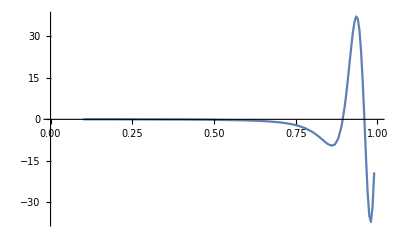

```mathematica
ListLinePlot[Transpose@{Transpose[%22][[1]],-Transpose[%22][[2]]},PlotRange->{{0,1},Automatic}]
```

#### 2→2

```mathematica
ωt2=B2π2toB0π0[√2000,√0.3136]
```

Wavefunction build complete.

M1=48.0754  M2=4.53486  M3=46.0366  M4=1.77918

z=0.109154    ω=0.1

z=0.152882    ω=0.14

z=0.196659    ω=0.18

z=0.240492    ω=0.22

z=0.284392    ω=0.26

z=0.328373    ω=0.3

z=0.372452    ω=0.34

z=0.416654    ω=0.38

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.384315}. NIntegrate obtained -4.43216×10^211+4.48914×10^125 ⅈ and 9.53969×10^211 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.672023}. NIntegrate obtained -7.56213×10^240+1.26904×10^127 ⅈ and 9.67669×10^240 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00148127,0.469104}. NIntegrate obtained -4.36785×10^220+2.19547×10^126 ⅈ and 8.4139×10^220 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.564323}. NIntegrate obtained -1.60894×10^231+1.91563×10^126 ⅈ and 1.00986×10^232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.36333}. NIntegrate obtained 9.47539×10^7 and 9.33126×10^7 for the integral and error estimates.

z=0.295379    ω=0.27

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.666648,0.446678}. NIntegrate obtained 1.23744×10^9 and 6.21225×10^9 for the integral and error estimates.

z=0.339382    ω=0.31

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.404628}. NIntegrate obtained -8.76018×10^212+6.60415×10^125 ⅈ and 4.44209×10^212 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.491859}. NIntegrate obtained -5.92301×10^222+3.32924×10^126 ⅈ and 9.00015×10^222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99999577011329322772809080361461342434381549537647515535354614258,0.99996508158169051045440498329264222832080122316256165504455566406}. NIntegrate obtained -1.57007×10^169+3.77048×10^123 ⅈ and 2.93461×10^169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99992263122388513681853584869063666928923339582979679107666015625,0.999857200854876567428820843819181618528091348707675933837890625}. NIntegrate obtained 588.832 and 322.312 for the integral and error estimates.

z=0.38349    ω=0.35

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.666648,0.112255}. NIntegrate obtained 1.35076×10^6 and 549904. for the integral and error estimates.

z=0.120082    ω=0.11

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99998913410316162934581365757252813253330714360345155000686645508,0.99995467927064971398282101563981250080814788816496729850769042969}. NIntegrate obtained -1.27673×10^188+5.98589×10^124 ⅈ and 2.53799×10^187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.9830825907689102784170476212466383003629744052886962890625,0.924542}. NIntegrate obtained 893.354 and 1883.3 for the integral and error estimates.

z=0.207611    ω=0.19

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00861255,0.589988}. NIntegrate obtained -3.47718×10^233+3.02383×10^126 ⅈ and 1.59816×10^233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99407827515412936110472674755555999581702053546905517578125,0.98739659256957546494548605409136143862269818782806396484375}. NIntegrate obtained -27417.4 and 195203. for the integral and error estimates.

z=0.350399    ω=0.32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.515293}. NIntegrate obtained -1.72529×10^225+7.91979×10^125 ⅈ and 2.56394×10^225 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.9898231970554963489450361890931162633933126926422119140625,0.984369324172842209696998594381511793471872806549072265625}. NIntegrate obtained 68591.4 and 149484. for the integral and error estimates.

z=0.427727    ω=0.39

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99990073923939741602404628062483737949150963686406612396240234375,0.9996779859113486862011270506211957354025798849761486053466796875}. NIntegrate obtained -3.34907×10^197+1.63268×10^125 ⅈ and 5.85438×10^196 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.701194}. NIntegrate obtained -1.17163×10^244+2.08171×10^127 ⅈ and 1.12942×10^244 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99998554892997199890423130376471139157956713461317121982574462891,0.99991876369408679596430689767716515348183747846633195877075195312}. NIntegrate obtained 6.20733×10^178+1.52767×10^124 ⅈ and 1.04841×10^180 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.165267}. NIntegrate obtained 5.72465×10^6 and 1.73952×10^6 for the integral and error estimates.

z=0.163822    ω=0.15

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99999381828956477977621145666192736811694885545875877141952514648,0.99995418261157364090416840157748978867857658769935369491577148437}. NIntegrate obtained -1.82592×10^171+8.81291×10^123 ⅈ and 1.39389×10^171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9806095223097069969730998906243257806636393070220947265625,0.9658457676953305093281443305386346764862537384033203125}. NIntegrate obtained 8649.62 and 1799.81 for the integral and error estimates.

z=0.394536    ω=0.36

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.616466}. NIntegrate obtained -2.3511×10^237+4.82726×10^126 ⅈ and 3.21402×10^236 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.98944649533897022393447162613711043377406895160675048828125,0.97246616140961004981502213695421232841908931732177734375}. NIntegrate obtained 4886.91 and 2443.77 for the integral and error estimates.

z=0.306371    ω=0.28

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.666648,0.594589}. NIntegrate obtained 6.4564×10^13 and 1.08451×10^13 for the integral and error estimates.

z=0.405591    ω=0.37

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99998738263303352149126825097052995161561739223543554544448852539,0.99995077953217964364677951966120517113267851527780294418334960937}. NIntegrate obtained -3.17775×10^190+8.2896×10^124 ⅈ and 1.87443×10^190 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00148127,0.425517}. NIntegrate obtained -3.24859×10^215+9.78857×10^125 ⅈ and 4.47225×10^215 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.403674}. NIntegrate obtained 7.24235×10^7 and 1.15976×10^8 for the integral and error estimates.

z=0.317369    ω=0.29

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.643794}. NIntegrate obtained -5.83363×10^238+7.78583×10^126 ⅈ and 4.28506×10^237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.446998}. NIntegrate obtained -2.53891×10^218+1.4621×10^126 ⅈ and 1.71317×10^217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.666648,0.424827}. NIntegrate obtained 6.30287×10^7 and 1.93662×10^7 for the integral and error estimates.

z=0.46101    ω=0.42

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99755554691608839569527678037275109090842306613922119140625,0.99156087620341077336350021909083807258866727352142333984375}. NIntegrate obtained 1953.16 and 4880.63 for the integral and error estimates.

z=0.25146    ω=0.23

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.794849}. NIntegrate obtained -1.05963×10^256+9.88712×10^127 ⅈ and 1.47991×10^255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.666648,0.779239}. NIntegrate obtained 4.51144×10^10 and 7.54898×10^9 for the integral and error estimates.

z=0.472128    ω=0.43

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.9997368530342554426870206596422718803296447731554508209228515625,0.999465758889993060166793970022780513318139128386974334716796875}. NIntegrate obtained 1302.76 and 1007.98 for the integral and error estimates.

z=0.361422    ω=0.33

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.828296}. NIntegrate obtained -1.34063×10^256+1.76482×10^128 ⅈ and 2.85369×10^256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.814594}. NIntegrate obtained 7.27574×10^8 and 3.64508×10^8 for the integral and error estimates.

z=0.48326    ω=0.44

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99878572999531556775472396214610171227832324802875518798828125,0.99028430504627292831065776823606938705779612064361572265625}. NIntegrate obtained 520.002 and 388.548 for the integral and error estimates.

z=0.131013    ω=0.12

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.539436}. NIntegrate obtained -4.01943×10^227+1.22615×10^126 ⅈ and 3.72757×10^227 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.9828394281004183864747236754055847995914518833160400390625,0.9748146832624704216652133936804602853953838348388671875}. NIntegrate obtained 8848.3 and 2874.26 for the integral and error estimates.

z=0.438811    ω=0.4

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.516773}. NIntegrate obtained 6.52374×10^10 and 8.37332×10^10 for the integral and error estimates.

z=0.505565    ω=0.46

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.995310170152388423193967614821531242341734468936920166015625,0.9804412342200654432999851195518203894607722759246826171875}. NIntegrate obtained 3682.23 and 3031.74 for the integral and error estimates.

z=0.218568    ω=0.2

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.731353}. NIntegrate obtained -3.31889×10^248+3.26753×10^127 ⅈ and 7.83241×10^248 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99999245067214483651860627974258810546359654836123809218406677246,0.99996082447515402375322812397739902223747776588425040245056152344}. NIntegrate obtained -5.01577×10^182+2.16621×10^124 ⅈ and 1.15501×10^183 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00861255,0.862964}. NIntegrate obtained -2.08628×10^258+3.20395×10^128 ⅈ and 1.16146×10^258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.179389}. NIntegrate obtained 5.58548×10^6 and 4.72628×10^6 for the integral and error estimates.

z=0.174764    ω=0.16

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.666648,0.712772}. NIntegrate obtained 2.92918×10^8 and 1.86906×10^8 for the integral and error estimates.

z=0.449905    ω=0.41

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0249979,0.936233}. NIntegrate obtained -1.16819×10^265+1.10774×10^129 ⅈ and 2.01153×10^265 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.851493}. NIntegrate obtained 2.94641×10^8 and 1.60266×10^8 for the integral and error estimates.

z=0.494405    ω=0.45

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.930358}. NIntegrate obtained 1.15473×10^9 and 9.24937×10^8 for the integral and error estimates.

z=0.516742    ω=0.47

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.762554}. NIntegrate obtained -2.16268×10^250+5.63805×10^127 ⅈ and 2.39067×10^249 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.001924,0.898918}. NIntegrate obtained -4.16676×10^262+5.9084×10^128 ⅈ and 1.88201×10^262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.666648,0.745326}. NIntegrate obtained 2.66074×10^8 and 3.27561×10^8 for the integral and error estimates.

z=0.539149    ω=0.49

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00030625,0.974986}. NIntegrate obtained -2.1637×10^268+6.49794×10^129 ⅈ and 4.42282×10^268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.18473,0.890041}. NIntegrate obtained 1.84955×10^8 and 2.02106×10^8 for the integral and error estimates.

z=0.572918    ω=0.52

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.945938}. NIntegrate obtained -3.09365×10^275+9.94857×10^132 ⅈ and 5.00118×10^274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.429446,0.940513}. NIntegrate obtained 6.89469×10^9 and 1.40176×10^10 for the integral and error estimates.

z=0.550383    ω=0.5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.837818}. NIntegrate obtained -1.14347×10^287+3.54786×10^143 ⅈ and 2.03277×10^287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.821311}. NIntegrate obtained 9.78499×10^8 and 6.70958×10^8 for the integral and error estimates.

z=0.584224    ω=0.53

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.804489}. NIntegrate obtained -6.40961×10^290+1.90154×10^147 ⅈ and 2.77267×10^290 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99999880170264339054076844516810024243724797088361810892820358276,0.99999567746685609680266649786431476520931482809828594326972961426}. NIntegrate obtained 9.93399×10^192+9.93578×10^124 ⅈ and 8.03103×10^193 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.784484}. NIntegrate obtained 1.18843×10^9 and 7.86854×10^8 for the integral and error estimates.

z=0.595559    ω=0.54

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.255943}. NIntegrate obtained 1.29258×10^7 and 5.66042×10^6 for the integral and error estimates.

z=0.229528    ω=0.21

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.9748853840572809688336253231000227970071136951446533203125,0.95963508623739783576223061345444875769317150115966796875}. NIntegrate obtained 3708.47 and 11583.9 for the integral and error estimates.

z=0.606925    ω=0.55

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.908458}. NIntegrate obtained -9.69675×10^281+2.70459×10^136 ⅈ and 1.35165×10^281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.899234}. NIntegrate obtained 1.50147×10^8 and 7.7809×10^7 for the integral and error estimates.

z=0.561638    ω=0.51

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.772384}. NIntegrate obtained -1.11285×10^295+1.3259×10^151 ⅈ and 1.27284×10^295 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99971422184306366260676812718344308450468815863132476806640625,0.999124985887549094836813934339403431295068003237247467041015625}. NIntegrate obtained -2.04014×10^200+2.35529×10^125 ⅈ and 4.40691×10^200 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00148127,0.741443}. NIntegrate obtained -3.42535×10^299+3.93088×10^154 ⅈ and 2.66623×10^298 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.666648,0.748966}. NIntegrate obtained 5.04219×10^8 and 4.63236×10^8 for the integral and error estimates.

z=0.641245    ω=0.58

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.714683}. NIntegrate obtained 1.27076×10^9 and 2.34163×10^9 for the integral and error estimates.

z=0.618325    ω=0.56

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.001924,0.872447}. NIntegrate obtained -4.57124×10^285+8.6022×10^139 ⅈ and 4.56895×10^285 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9803710660742609127316082862080293125472962856292724609375,0.936126}. NIntegrate obtained 1679.9 and 3385.44 for the integral and error estimates.

z=0.262432    ω=0.24

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.666648,0.859535}. NIntegrate obtained 7.48775×10^8 and 1.24108×10^9 for the integral and error estimates.

z=0.675994    ω=0.61

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0249979,0.654975}. NIntegrate obtained -1.0723941113340878388997362773172298918641610185697347741760406869×10^314+3.19846×10^167 ⅈ and 1.6971475228915407570893286323391191402075953261828702274980747174×10^313 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.711601}. NIntegrate obtained -2.66002×10^305+2.84136×10^158 ⅈ and 6.14163×10^305 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0249979,0.345306}. NIntegrate obtained -2.02824×10^207+2.10347×10^125 ⅈ and 1.99464×10^207 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.57693}. NIntegrate obtained -5.5707209013494524262416248181824186561629297542695493741674856527×10^331+6.67198×10^182 ⅈ and 4.7976463202286674443897332031583375494162093153136823036065463365×10^331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.666648,0.325397}. NIntegrate obtained 3.47408×10^7 and 1.405×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.27341    ω=0.25

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.666648,0.531158}. NIntegrate obtained 8.35421×10^8 and 1.85676×10^9 for the integral and error estimates.

z=0.687702    ω=0.62

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99991016653349219083250689482644801842070592101663351058959960937,0.9995682759198508769552839192673587831450277008116245269775390625}. NIntegrate obtained -2.60465×10^183+3.0517×10^124 ⅈ and 1.81869×10^183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.193885}. NIntegrate obtained 1.07748×10^8 and 8.02904×10^7 for the integral and error estimates.

z=0.18571    ω=0.17

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99996872946496964656016692013507096703506249468773603439331054687,0.99978998783418392335667519710273865030103479512035846710205078125}. NIntegrate obtained -9.07759×10^173+1.22012×10^124 ⅈ and 5.5349×10^173 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.364547}. NIntegrate obtained -4.21321×10^208+3.0623×10^125 ⅈ and 1.03249×10^208 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.344074}. NIntegrate obtained 3.24639×10^7 and 3.29195×10^7 for the integral and error estimates.

z=0.711356    ω=0.64

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99092053591967231389314729739226095261983573436737060546875,0.934261}. NIntegrate obtained 184.852 and 83.9633 for the integral and error estimates.

z=0.141946    ω=0.13

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.552566}. NIntegrate obtained -1.1696236146629725032757047438633121899321896940196990643067869399×10^339+3.19642×10^188 ⅈ and 2.7562485449536385119269508365537402611148851767168661670651353198×10^339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.666648,0.503707}. NIntegrate obtained 1.46416×10^9 and 1.10372×10^9 for the integral and error estimates.

z=0.699485    ω=0.63

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.9867511388607700349717699594975783838890492916107177734375,0.98637740584407218764895208806819937308318912982940673828125}. NIntegrate obtained 95051.8 and 60242. for the integral and error estimates.

z=0.527936    ω=0.48

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.506076}. NIntegrate obtained -1.5972458255977712842274622405066684259579540064646076731165579056×10^354+8.85181×10^200 ⅈ and 3.7922386247976157402237431658826534236628989274422625327820203951×10^354 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.984969}. NIntegrate obtained -7.88302×10^273+1.53875×10^130 ⅈ and 1.86125×10^274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.666648,0.983467}. NIntegrate obtained 4.19303×10^8 and 2.28623×10^8 for the integral and error estimates.

z=0.747651    ω=0.67

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.528961}. NIntegrate obtained -1.3862517131660476322081835859505673507114438423963474980523059563×10^345+3.38728×10^194 ⅈ and 1.3269685911574211546786790602275721891776273065242486981802837063×10^345 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99987762889483369156055740656352526229966315440833568572998046875,0.99957873058932173999761860994084372578072361648082733154296875}. NIntegrate obtained 1.82698×10^194+1.52846×10^125 ⅈ and 8.35026×10^195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.477008}. NIntegrate obtained 5.82933×10^8 and 5.22553×10^8 for the integral and error estimates.

z=0.78551    ω=0.7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.441383}. NIntegrate obtained -1.3733550719047661736242867794873803594872639122994045630581747724×10^376+1.45547×10^223 ⅈ and 8.5224068963822965409060194473032296241085299957717901773759878148×10^375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.381919}. NIntegrate obtained -1.1025064440019069698343351182106196372232902057765590422585762872×10^408+8.04179×10^251 ⅈ and 1.6762461533740738066244512115384762151018839138109473338308698939×10^408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.376644}. NIntegrate obtained 9.69525×10^9 and 9.40661×10^9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.974805535302890109605744584087005932815372943878173828125,0.9828302434137319680551581058125520939938724040985107421875}. NIntegrate obtained 9643.72 and 125264. for the integral and error estimates.

z=0.629764    ω=0.57

z=0.760049    ω=0.68

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0249979,0.682796}. NIntegrate obtained -8.2231242022409795325477834388474466417513705547836856847134521983×10^310+7.57174×10^162 ⅈ and 1.9459402756564456153213770621026638104643796403904691576275167955×10^311 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.421028}. NIntegrate obtained -3.5837992191498376717567723118002854834246657103040846482533319215×10^385+6.93404×10^231 ⅈ and 3.4588127771979753852538254208217706949463019311847103218204824589×10^385 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.926963,0.9742237184489111780083536729080151417292654514312744140625}. NIntegrate obtained 503228. and 998687. for the integral and error estimates.

z=0.772653    ω=0.69

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9540686520147113880430111976238549686968326568603515625,0.9715906263266320570803902256784567725844681262969970703125}. NIntegrate obtained 35994.1 and 52186.3 for the integral and error estimates.

z=0.652773    ω=0.59

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.401218}. NIntegrate obtained -1.2958672624883807219395954284475906252361932362293709362444607261×10^397+2.2954×10^241 ⅈ and 1.1839694311715650200950849229444044522374681814444606762680393866×10^397 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.628089}. NIntegrate obtained -7.613172107738922899942031868976617954276034553663373563342744902×10^321+2.26284×10^172 ⅈ and 7.5916410705072710764765630231949006863776411462012493382573435511×10^321 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.860755,0.95411872738368319613044832294690422713756561279296875}. NIntegrate obtained -8481.55 and 140379. for the integral and error estimates.

z=0.826492    ω=0.73

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.588519}. NIntegrate obtained 1.08257×10^9 and 7.07147×10^8 for the integral and error estimates.

z=0.664354    ω=0.6

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9913063831291803428003017728542545228265225887298583984375,0.99607930647661024371741778082878226996399462223052978515625}. NIntegrate obtained 945908. and 133856. for the integral and error estimates.

z=0.723329    ω=0.65

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99470853694427083420415147685389456455595791339874267578125,0.9805881405947140493084557277825297205708920955657958984375}. NIntegrate obtained 5222.58 and 8525.85 for the integral and error estimates.

z=0.87746    ω=0.76

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.326682}. NIntegrate obtained -1.4285687483492493135244433085311187257995154064705192972714799427×10^455+5.29746×10^292 ⅈ and 2.8857130753636279945835714765108406069407387687883848243506772637×10^455 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0249979,0.602088}. NIntegrate obtained -7.7895827510597881734125128071980774505381861995597849485521308785×10^325+2.84076×10^177 ⅈ and 7.4586984801788030601735718028353100386473040667111002944181941788×10^325 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.483875}. NIntegrate obtained -1.517857278220185223820847572151527913748356716069624952271073207×10^360+6.45083×10^207 ⅈ and 3.5545409420746457569509751292143380716757189332148448591873960151×10^360 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.893245,0.9746230510943419377001273318228413700126111507415771484375}. NIntegrate obtained 147032. and 268037. for the integral and error estimates.

z=0.841553    ω=0.74

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.666648,0.55941}. NIntegrate obtained 2.14402×10^10 and 2.11582×10^10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99992000881920330321273818890981388562977372203022241592407226562,0.9996424792721216417133202336575692470432841219007968902587890625}. NIntegrate obtained -8.087×10^185+4.28519×10^124 ⅈ and 1.56744×10^185 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.308956}. NIntegrate obtained -7.57710696683040425613608994378627508307785312273881468616173362×10^477+5.74751140452479×10^310 ⅈ and 9.268924870463415161478764531908907930495400635432418021699380352×10^476 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99994724996213014358464096081879901589672954287379980087280273437,0.9996765476017330661305526628979123415774665772914886474609375}. NIntegrate obtained -3.04361×10^176+1.63299×10^124 ⅈ and 4.57266×10^176 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.208774}. NIntegrate obtained 3.10719×10^7 and 3.52591×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.972382557876295926246879020027336082421243190765380859375,0.99153851919397321089399977012135423137806355953216552734375}. NIntegrate obtained 69848.2 and 78769.8 for the integral and error estimates.

z=0.79869    ω=0.71

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.363098}. NIntegrate obtained -1.2849108246288177370081894881474359355568135208406628654566689629×10^423+5.29152×10^263 ⅈ and 1.0634549962908204750789392171245718611342525307868404217332745165×10^422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.894004,0.9699423598392112912114360057103112922050058841705322265625}. NIntegrate obtained 57981.9 and 45045.3 for the integral and error estimates.

z=0.812297    ω=0.72

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.95643091696727071393535624110882054083049297332763671875,0.971701449647801578091144136806178721599280834197998046875}. NIntegrate obtained 27182.6 and 24447.7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.344703}. NIntegrate obtained -5.2509822325978226509730036860343997667856608066383162573557166693×10^436+1.20904×10^277 ⅈ and 2.2886391084385098948179531077226564581998923028079989808523444102×10^436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.836639,0.957406814895251791208696801049882196821272373199462890625}. NIntegrate obtained -32389.7 and 270053. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.996853517560141832824782692767939806799404323101043701171875,0.979210945415807269831542924976020003668963909149169921875}. NIntegrate obtained -443.77 and 6401.08 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.9996559832029120116190547273848920895034098066389560699462890625,0.99990585578387404957253613985157514321144844871014356613159179687}. NIntegrate obtained -3.3401136141347829867820497401309995355842030857603426586556449266×10^539+3.97666516738434×10^366 ⅈ and 2.3627009747236819464571692314545294672111279396301440815678447806×10^539 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.989960076115342098301841389229593914933502674102783203125,0.995726037805001661269710400148369444650597870349884033203125}. NIntegrate obtained 54549.2 and 21096.7 for the integral and error estimates.

z=0.73542    ω=0.66

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9833015622295583069156776900854310952126979827880859375,0.9964264870998159055910659009924756901455111801624298095703125}. NIntegrate obtained 60156.6 and 44137.1 for the integral and error estimates.

z=0.858042    ω=0.75

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.895839,0.983203514390001497014193176937624230049550533294677734375}. NIntegrate obtained 65016.7 and 58353.6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.462322}. NIntegrate obtained -7.2086112825787427049788601941692533769169116450604373912065114072×10^367+1.54286×10^215 ⅈ and 1.6292886690896477033808762837437127499236245723403883582246397142×10^368 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.291362}. NIntegrate obtained -6.2270030170151487939499574057723681573338368604974011374585449281×10^503+1.69421792456857×10^333 ⅈ and 3.5762581099076244818184308731148379455209940095308017246864958641×10^503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.666648,0.400882}. NIntegrate obtained 1.23842×10^9 and 1.00825×10^9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.926908,0.98616408406434603699242114061007669079117476940155029296875}. NIntegrate obtained -34426.4 and 538170. for the integral and error estimates.

{{0.1,1.20332×10^7+0. ⅈ},{0.11,4159.63+0. ⅈ},{0.12,1338.62+0. ⅈ},{0.13,-2929.07+0. ⅈ},{0.14,3.46389×10^7},{0.15,3.11364×10^7+0. ⅈ},{0.16,5.55737×10^8+0. ⅈ},{0.17,1.48833×10^8+0. ⅈ},{0.18,3987.05+0. ⅈ},{0.19,15356.6+0. ⅈ},{0.2,5.05032×10^7},{0.21,19161.2},{0.22,6742.91+0. ⅈ},{0.23,5467.26+0. ⅈ},{0.24,1.06765×10^8+0. ⅈ},{0.25,9.43518×10^7+0. ⅈ},{0.26,2.60795×10^8+0. ⅈ},{0.27,12753.4+0. ⅈ},{0.28,1.79411×10^8+0. ⅈ},{0.29,1.48363×10^8+0. ⅈ},{0.3,2.77034×10^9+0. ⅈ},{0.31,-58427.1+0. ⅈ},{0.32,2644.6+0. ⅈ},{0.33,1.2624×10^11+0. ⅈ},{0.34,1086.82+0. ⅈ},{0.35,15235.9+0. ⅈ},{0.36,1.08587×10^14+0. ⅈ},{0.37,5957.7+0. ⅈ},{0.38,105296.+0. ⅈ},{0.39,12983.7+0. ⅈ},{0.4,4.10956×10^8+0. ⅈ},{0.41,3.56991×10^8+0. ⅈ},{0.42,5.78957×10^10+0. ⅈ},{0.43,8.93176×10^8+0. ⅈ},{0.44,3.46029×10^8+0. ⅈ},{0.45,2.07805×10^8+0. ⅈ},{0.46,1.24117×10^9+0. ⅈ},{0.47,97733.+0. ⅈ},{0.48,4.1237×10^8+0. ⅈ},{0.49,6.48454×10^9+0. ⅈ},{0.5,1.35018×10^8+0. ⅈ},{0.51,6.43596×10^8+0. ⅈ},{0.52,8.03652×10^8+0. ⅈ},{0.53,9.32303×10^8+0. ⅈ},{0.54,3.77643×10^8+0. ⅈ},{0.55,9.08188×10^8+0. ⅈ},{0.56,6572.79+0. ⅈ},{0.57,17656.1+0. ⅈ},{0.58,22263.9+0. ⅈ},{0.59,6.37114×10^8+0. ⅈ},{0.6,1.19939×10^10+0. ⅈ},{0.61,4.4374×10^8+0. ⅈ},{0.62,7.37506×10^8+0. ⅈ},{0.63,2.78064×10^8+0. ⅈ},{0.64,426610.+0. ⅈ},{0.65,23218.8+0. ⅈ},{0.66,4.96455×10^8+0. ⅈ},{0.67,3.65163×10^9+0. ⅈ},{0.68,177573.+0. ⅈ},{0.69,-2794.58+0. ⅈ},{0.7,21402.5+0. ⅈ},{0.71,16439.9+0. ⅈ},{0.72,-8443.95+0. ⅈ},{0.73,34946.9+0. ⅈ},{0.74,12880.5+0. ⅈ},{0.75,-6516.16+0. ⅈ},{0.76,10483.1+0. ⅈ},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
ωt2=B2π2toB0π0[√2000,1]
```

Wavefunction build complete.

M1=48.3531  M2=5.208  M3=46.4407  M4=2.69713

z=0.99859    ω=0.1

z=0.996789    ω=0.2

z=0.994406    ω=0.3

z=0.991092    ω=0.4

z=0.986141    ω=0.5

z=0.986141    ω=0.5

z=0.98413    ω=0.53

z=0.981752    ω=0.56

z=0.978889    ω=0.59

z=0.975357    ω=0.62

z=0.970855    ω=0.65

z=0.964828    ω=0.68

z=0.95942    ω=0.7

z=0.952052    ω=0.72

z=0.940639    ω=0.74

Overflow

Overflow

Overflow

«19 more identical outputs»

z=0.931519    ω=0.99

Overflow

z=0.931118    ω=0.75

z=0.947106    ω=0.73

z=0.956059    ω=0.71

{{0.1,-2.42495×10^-7},{0.2,-1.57795×10^-6},{0.3,-6.35978×10^-6},{0.4,-0.0000292324},{0.5,-0.000162409},{0.5,-0.000162409},{0.53,-0.000296952},{0.56,-0.000576695},{0.59,-0.00122244},{0.62,-0.00290086},{0.65,-0.00802187},{0.68,-0.0273786},{0.7,-0.0728083},{0.71,-0.12637},{0.72,-0.231357},{0.73,-0.453425},{0.74,-0.975846},{0.75,-2.46465},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,{0.99,-2.87094-0.0000895198 ⅈ}}

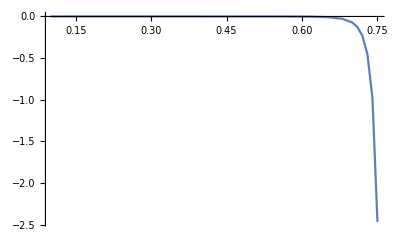

```mathematica
ListPlot[Chop[ωt2,10^-5],Joined->True,PlotRange->All]
```

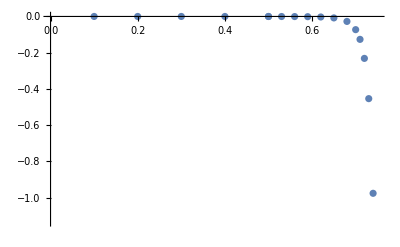

```mathematica
ListPlot[Chop[ωt2,10^-5]]
```

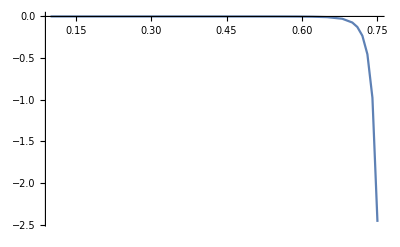

```mathematica
ListPlot[Chop[ωt2,10^-5],Joined->True,PlotRange->All]
```

#### Debug

```mathematica
Block[{mQ=√2000,mq=√0.3136},m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
ΦB[x_]=ϕxB;
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
ΦB[x_]=ϕxB;
}
];
m1=mq;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Valsπ,ϕxπ}=Determineϕx[m1,m2,β,Nx];
Φπ[x_]=ϕxπ;
Export[dir<>filename,{Valsπ,ϕxπ}]
},
{
{Valsπ,ϕxπ}=Import[dir<>filename];
Φπ[x_]=ϕxπ;
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
{M2,ϕ2}={Mn[#][Valsπ],ϕn[#][Φπ]}&[2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][Valsπ],ϕn[#][Φπ]}&[0];]
```

Wavefunction build complete.

```mathematica
Solve[-4 (M3^2-M3^2 ω+M4^2 ω) (M1^2 ω-M1^2 ω^2)+(-M3^2-M1^2 ω+M2^2 ω+M3^2 ω-M4^2 ω+M1^2 ω^2-M2^2 ω^2)^2==0,ω]
```

{{ω→0.769533},{ω→0.995038},{ω→1.01678},{ω→1.09949}}

```mathematica
zfp[0.5][M1,M2,M3,M4]
```

0.550383

```mathematica
FBBplusDD[zfp[0.5][M1,M2,M3,M4],0.5][ϕ1,ϕ2,ϕ3,ϕ4]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.908458}. NIntegrate obtained -9.69675×10^281+2.70459×10^136 ⅈ and 1.35165×10^281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.899234}. NIntegrate obtained 1.50147×10^8 and 7.7809×10^7 for the integral and error estimates.

1.35018×10^8+0. ⅈ

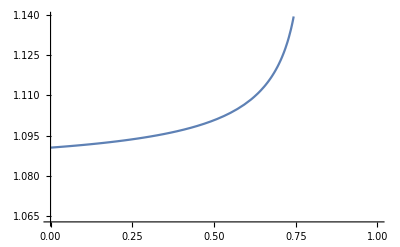

```mathematica
Plot[(zfp[x][M1,M2,M3,M4])/x,{x,0,1}]
```

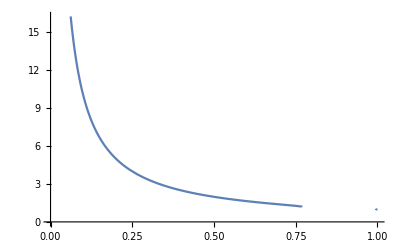

```mathematica
Plot[(zfn[x][M1,M2,M3,M4])/x,{x,0,1}]
```

```mathematica
Block[{ω=0.5,z=zfn[0.5][M1,M2,M3,M4]},(1+ℂ)(-HeavisideTheta[ω-z](1-ω)/z NIntegrate[ϕ2[(1-ω)/(1-z)x]ϕ4[x](ϕ1[y]ϕ3[z/ω y])/(y-(1-(1-x)(1-ω)/z))^2,{x,0,1},{y,0,1}]+HeavisideTheta[z-ω](1-z)/ω NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1}])]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.429446,0.505447}. NIntegrate obtained -2.1966165922340522940645389258927885619810148089581012431095580253×10^1510-5.2620286429825031327227159853958633720500447933640082518197173772×10^1116 ⅈ and 3.1572785222006068667743552541392232451608506631397822336978961747×10^1510 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.806499,0.995829857886447255589656979424262317479588091373443603515625}. NIntegrate obtained 860.196 and 941.808 for the integral and error estimates.

18.5365+0. ⅈ

```mathematica
Block[{ω=0.5,z=zfp[0.5][M1,M2,M3,M4]},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.899234}. NIntegrate obtained 1.50147×10^8 and 7.7809×10^7 for the integral and error estimates.

1.50147×10^8

```mathematica
Block[{ω=0.5,z=zfp[0.5][M1,M2,M3,M4]},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1},Method->"LocalAdaptive"]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.79153,0.812538}. NIntegrate obtained 0.281929 and 0.623145 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.791534,0.812538}. NIntegrate obtained 0.0916072 and 0.0854258 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.791534,0.812541}. NIntegrate obtained 0.0295885 and 0.0310185 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

2.05784×10^12

```mathematica
Block[{ω=0.5,z=zfp[0.5][M1,M2,M3,M4]},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1},Method->"MonteCarlo",MaxPoints->10^8]]
```

NIntegrate::maxp: The integral failed to converge after 100000100 integrand evaluations. NIntegrate obtained 2.92895×10^7 and 1.31099×10^7 for the integral and error estimates.

2.92895×10^7

```mathematica
Block[{ω=0.5,z=zfn[0.5][M1,M2,M3,M4],x=0.5},Print[z];NIntegrate[(ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{y,0,1-(1-x)(1-ω)/z,1},Method->{"PrincipalValue"}]]
```

0.989225

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.989386}. NIntegrate obtained -21594.5 and 19923.7 for the integral and error estimates.

-21594.5

```mathematica
Block[{ω=0.5,z=zfn[0.5][M1,M2,M3,M4],x=0.5},Print[z];NIntegrate[(ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{y,0,1},Method->"LocalAdaptive"]]
```

0.989225

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.989225}. NIntegrate obtained -973.157 and 5.96569×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.989225}. NIntegrate obtained -876.1 and 6.29143×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.989225}. NIntegrate obtained -1001.86 and 8.52305×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-4.00256×10^8

```mathematica
Block[{ω=0.9,z=zfp[0.9][M1,M2,M3,M4],x=0.4},1-(1-x)(1-ω)/z]
```

0.93929-0.00561497 ⅈ

```mathematica
Block[{ω=0.},1/(1-ω)NIntegrate[ϕ1[x]ϕ2[x/ω] ϕ3[p]/(p-(x-ω)/(1-ω))^2,{p,0,1},{x,0,ω},Method->"GlobalAdaptive"]-1/ω NIntegrate[ϕ1[x]ϕ3[(x-ω)/(1-ω)] ϕ2[p]/(p-x/ω)^2,{p,0,1},{x,ω,1},Method->"GlobalAdaptive"]]
```